```mathematica
f[x_,r1_,r2_]:=π*Mean[{r1,r2}]^2-(r1^2*ArcCos[(x^2+r1^2-r2^2)/(2*x*r1)]+r2^2*ArcCos[(x^2+r2^2-r1^2)/(2*x*r2)]-1/2*Sqrt[(-x+r1+r2)*(x+r1-r2)*(x-r1+r2)*(x+r1+r2)]);
f[x_,r_]:=π*r^2-(r^2*ArcCos[x^2/(2*x*r)]+r^2*ArcCos[x^2/(2*x*r)]-1/2*Sqrt[(-x+2*r)*x*x*(x+2*r)]);
```

```mathematica
g[x_]:=(1-1/16*(4+x)*(2-x)^2);
g[x_,r_]:=r^2*π*g[x/r];
```

```mathematica
xl=Row[{Style["Separation distance between particles Δ",FontFamily->"Latin Modern Roman",Plain,18],Style["r",FontFamily->"Latin Modern Roman",Italic,18]}]
yl=DisplayForm[Row[{Style["Distance ",FontFamily->"Latin Modern Roman",Plain,18],DisplayForm@SuperscriptBox[SubscriptBox[Style["d",FontFamily->"Latin Modern Roman",Italic,18],Style["Euler",FontFamily->"Latin Modern Roman",Plain,12]],Style["2",FontFamily->"Latin Modern Roman",Plain,12]],Style["(Δ",FontFamily->"Latin Modern Roman",Plain,18],
Style["r",FontFamily->"Latin Modern Roman",Italic,18],
Style[")",FontFamily->"Latin Modern Roman",Plain,18],
Style[" [",FontFamily->"Latin Modern Roman",Plain,18],SuperscriptBox[Style["m",FontFamily->"Latin Modern Roman",Plain,18],Style["dim",FontFamily->"Latin Modern Roman",Plain,12]],Style["]",FontFamily->"Latin Modern Roman",Plain,18]}]]
pl[dim_]:=Row[{DisplayForm[Style["dim",16,FontFamily->"Latin Modern Roman",Plain]],Style["="<>ToString[dim],FontFamily->"Latin Modern Roman",Plain,16]}];
```

Separation distance between particles Δr

Distance d_Euler^2(Δr) [m^dim]

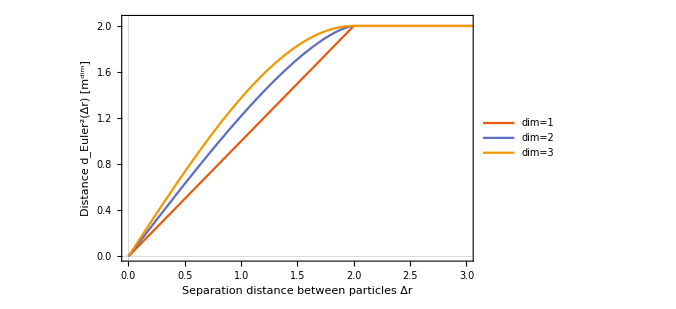

```mathematica
graphics=Plot[{2*If[x≤2,x/2,1],2*1/π*f[x,1],2*If[x≤2,1/π*g[x,1],1]},{x,0,4},
PlotRange->{{0,3},{0,2.05}},
ColorFunctionScaling->False,
PlotTheme->"Scientific",
FrameStyle->Directive[Black,FontColor->Black,15,FontFamily->"Latin Modern Roman",Plain],
FrameLabel->{xl,yl},
PlotLegends->Placed[LineLegend[Automatic,{pl[1],pl[2],pl[3]},LegendLayout->"Column"],{5/6+0.02,0.255}],
ImageSize->{500,500./GoldenRatio},
PlotRangePadding->0]
```

```mathematica
Export["/home/tm/Projects/hzdr_presentation/images/box_filter_distance.png",graphics,ImageResolution->300];
```